```mathematica
h:=1/2(k11 Jx^(3/2) Sqrt[Jy]+k12 Sqrt[Jx] Jy^(3/2))(Cos[ϕx-ϕy+η n 2π])+3/8(p Jx^2+r Jy^2+2 q Jx Jy)+3/4f2 Jx Jy (Cos[2ϕx-2ϕy+2η n 2π])+k1 Cos[ϕx+2 π s(νx+νy+η)/2-wr s]Sqrt[Jx]+k2 Cos[ϕy+2 π s(νx+νy-η)/2-wr s]Sqrt[Jy]
ϕxstr=D[h,Jx];
Jxstr=-D[h,ϕx];
ϕystr=D[h,Jy];
Jystr=-D[h,ϕy];
Jxstrd=Jxstr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
Jystrd=Jystr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
ϕxstrd=ϕxstr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
ϕystrd=ϕystr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
```

```mathematica
inputpr=({Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==Jxv,Jy[0]==Jyv,ϕx[0]==ϕxv,ϕy[0]==ϕyv}/.{f2->f2,k11->k11,k12->k12,p->p,r->r,q->q,η->η,n->t,k1->k1,k2->k2,νx->νx,νy->νy,wr->wr,s->t});
```

```mathematica
ситуация k11=-k12:
```

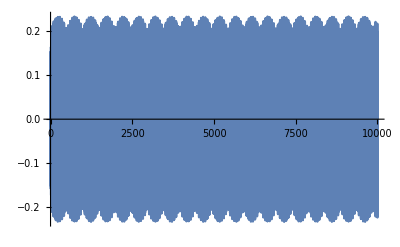

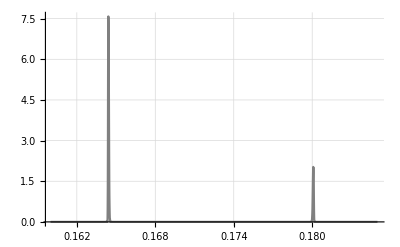

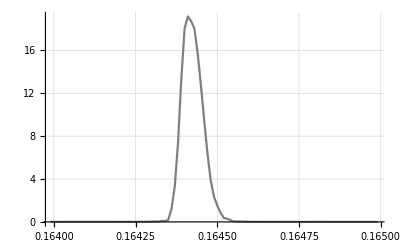

```mathematica
inloc=inputpr/.{Jxv->a^2/100,Jyv->b^2/100,ϕxv->ϕa,ϕyv->ϕb,f2->0,k11->-50,k12->50,p->0,r->0,q->-0,η->0.001,k1->.0,k2->.0,νx->.1705,νy->.1695,wr->.1715,n->t};
tablesol=Flatten[NDSolve[inloc/.{a->0.15,b->.5,ϕa->π,ϕb->0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,100000}]];
podsum=(10(Sqrt[Jx[t]/.(tablesol)]/.{t->t1})Cos[2π νx0 n+ϕa+(ϕx[t]/.(tablesol))/.{t->t1}])/.{νx0->0.1705,n->t1,ϕa->π,ϕb->0};
tablea=Table[{t1,podsum},{t1,0,100000,1}];
ListPlot[tablea[[Range[10000]]],Joined->True,PlotRange->All]
podsumb=(10(Sqrt[Jy[t]/.(tablesol)]/.{t->t1})Cos[2π νy0 n+ϕb+(ϕy[t]/.(tablesol))/.{t->t1}])/.{νy0->0.1695,n->t1,ϕa->π,ϕb->0};
tableb=Table[{t1,podsumb},{t1,0,100000,1}];
x= tablea[[All,2]];
y=tableb[[All,2]];
xwind=Table[(Sin[i π/100000])^2 x[[i]],{i,0,100000}];
ywind=Table[(Sin[i π/100000])^2 y[[i]],{i,0,100000}];
listfourierx=Abs[Fourier[xwind/.{wx->10,γ->π/4,wy->10}]];
listfouriery=Abs[Fourier[ywind/.{wx->10,γ->π/4,wy->10,α->0}]];
fur110a=ListPlot[Table[{(n1-1)/(100000),listfourierx[[n1]]},{n1,1,100001}][[Range[16000,18500]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic] 
fur110b=ListPlot[Table[{(n1-1)/(100000),listfouriery[[n1]]},{n1,1,100001}][[Range[16400,16500]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic]
```

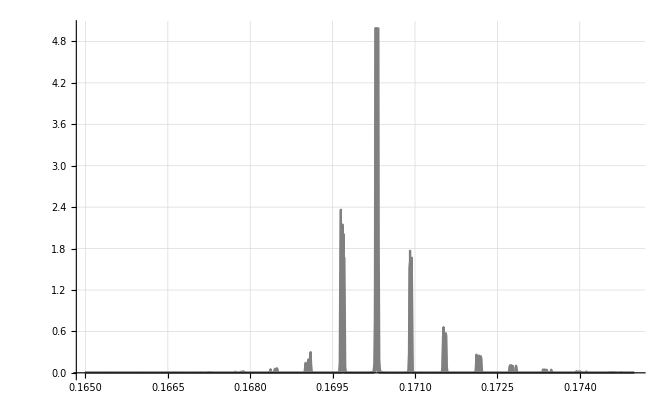

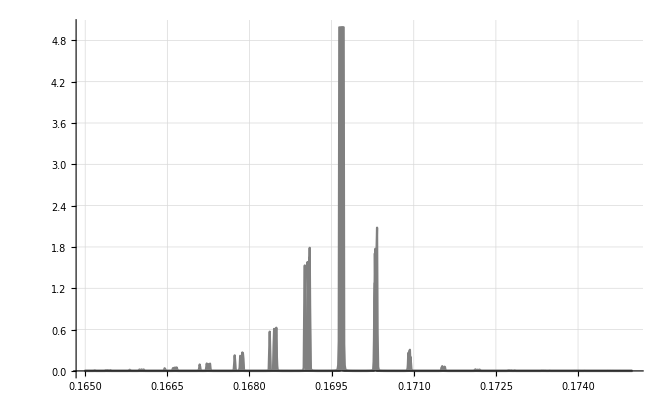

```mathematica
Show[{furm1a,fur00a,fur1a,fur2a}]
Show[{furm1b,fur00b,fur1b,fur2b}]
```

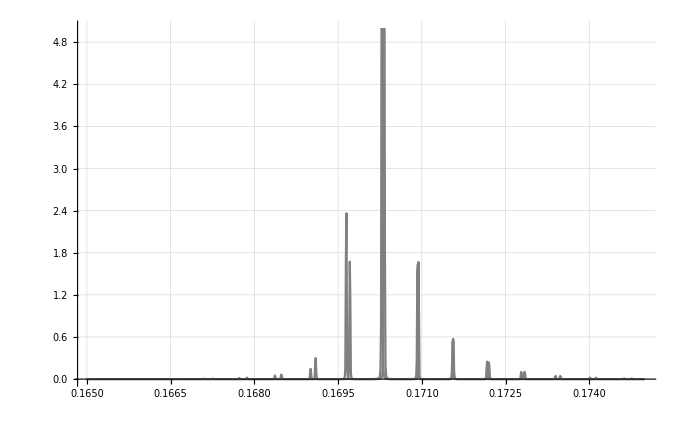

```mathematica
Show[{furm1a,fur2a}]
```

```mathematica
Show[{furm1b,fur2b}]
```

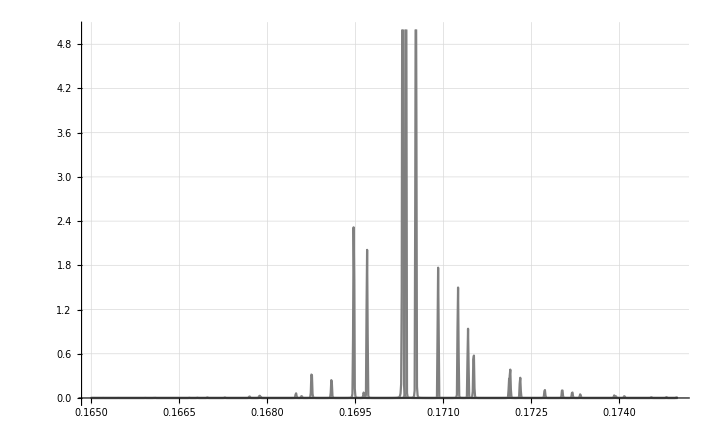

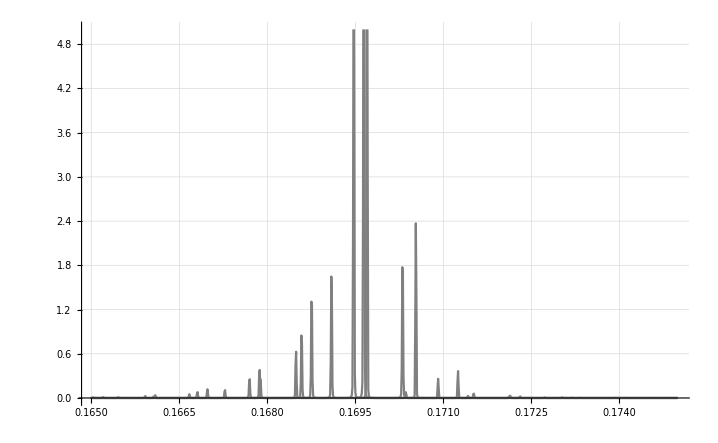

```mathematica
Show[{furm11a,fur0a,fur11a,fur12a}]
Show[{furm11b,fur0b,fur11b,fur12b}]
```

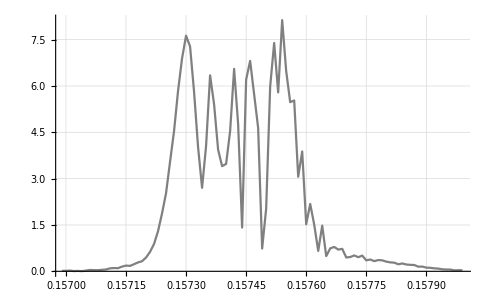

```mathematica
Show[fur12a]
```

```mathematica
Show[fur
```

```mathematica
inloc=inputpr/.{Jxv->a^2/100,Jyv->b^2/100,ϕxv->ϕa,ϕyv->ϕb,f2->50,k11->-50,k12->50,p->0,r->0,q->0,η->0.001,k1->.0,k2->.0,νx->.1705,νy->.1695,wr->.1715,n->t};
tablesol=Flatten[NDSolve[inloc/.{a->0.1,b->.1,ϕa->π,ϕb->0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,100000}]];
```

```mathematica
podsum=(10(Sqrt[Jx[t]/.(tablesol)]/.{t->t1})Cos[2π νx0 n+ϕa+(ϕx[t]/.(tablesol))/.{t->t1}])/.{νx0->0.1705,n->t1,ϕa->π,ϕb->0};
```

```mathematica
tablea=Table[{t1,podsum},{t1,0,100000,1}];
```

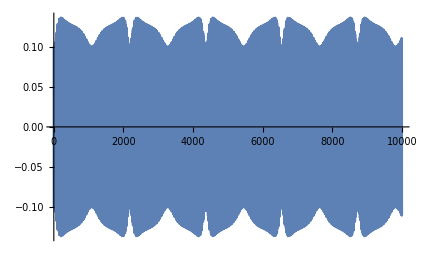

```mathematica
ListPlot[tablea,Joined->True,PlotRange->All]
```

```mathematica
podsumb=(10(Sqrt[Jy[t]/.(tablesol)]/.{t->t1})Cos[2π νy0 n+ϕb+(ϕy[t]/.(tablesol))/.{t->t1}])/.{νy0->0.1695,n->t1,ϕa->π,ϕb->0};
```

```mathematica
tableb=Table[{t1,podsumb},{t1,0,100000,1}];
```

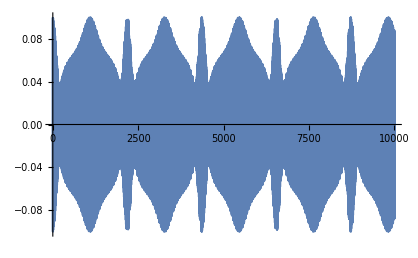

```mathematica
ListPlot[tableb,Joined->True,PlotRange->All]
```

```mathematica
но переход в x-y почему то меняет "η", что на самом деле не сильно страшно - пики все равно отстают друг от друга на (новую) η
```

```mathematica
a1=wx Cos[γ];
a1c=wx Cos[γ];
a3=wy Sin[γ] ;
a3c=wy Sin[γ];
b1=-Sin[γ]wx ;
b1c=-Sin[γ]wx ;
b3=wy Cos[γ];
b3c=wy Cos[γ] ;
```

```mathematica
x=a1 tablea[[All,2]]+b1 tableb[[All,2]];
y=a3 tablea[[All,2]]+b3 tableb[[All,2]];
```

```mathematica
x= tablea[[All,2]];
y=tableb[[All,2]];
```

```mathematica
Show[{ploty,plotx}]
```

Show::gcomb: Could not combine the graphics objects in Show[{ploty,plotx}].

Show[{ploty,plotx}]

```mathematica
xwind=Table[(Sin[i π/100000])^2 x[[i]],{i,0,100000}];
ywind=Table[(Sin[i π/100000])^2 y[[i]],{i,0,100000}];
```

```mathematica
listfourierx=Abs[Fourier[xwind/.{wx->10,γ->π/4,wy->10}]];
listfouriery=Abs[Fourier[ywind/.{wx->10,γ->π/4,wy->10,α->0}]];
```

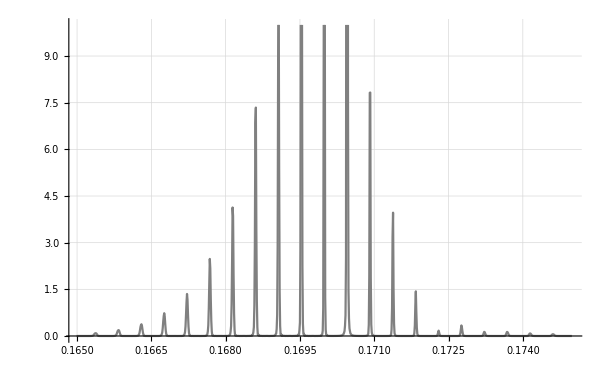

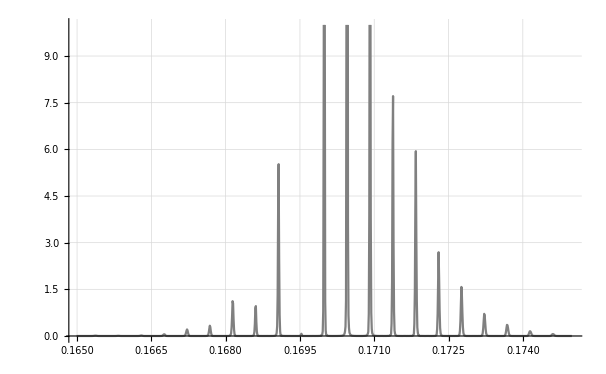

```mathematica
ListPlot[Table[{(n1-1)/(100000),listfourierx[[n1]]},{n1,1,100001}][[Range[16500,17500]]],PlotStyle->Gray,PlotRange->{0,10},Joined->True,GridLines->Automatic] 
ListPlot[Table[{(n1-1)/(100000),listfouriery[[n1]]},{n1,1,100001}][[Range[16500,17500]]],PlotStyle->Gray,PlotRange->{0,10},Joined->True,GridLines->Automatic]
```

```mathematica
хороший вариант для нас: более-менее разные и небольшие k11,k12, заметная f2: видны несколько пиков отстающих на η друг от друга
```

```mathematica
inloc=inputpr/.{Jxv->a^2/100,Jyv->b^2/100,ϕxv->ϕa,ϕyv->ϕb,f2->50,k11->-10,k12->-15,p->0,r->0,q->-0,η->0.001,k1->.0,k2->.0,νx->.1705,νy->.1695,wr->.1715,n->t};
tablesol=Flatten[NDSolve[inloc/.{a->0.1,b->.1,ϕa->π,ϕb->0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,100000}]];
```

```mathematica
podsum=(10(Sqrt[Jx[t]/.(tablesol)]/.{t->t1})Cos[2π νx0 n+ϕa+(ϕx[t]/.(tablesol))/.{t->t1}])/.{νx0->0.1705,n->t1,ϕa->π,ϕb->0};
```

```mathematica
tablea=Table[{t1,podsum},{t1,0,100000,1}];
```

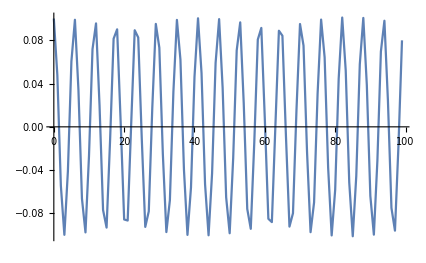

```mathematica
ListPlot[tablea[[Range[0,100]]],Joined->True,PlotRange->All]
```

```mathematica
podsumb=(10(Sqrt[Jy[t]/.(tablesol)]/.{t->t1})Cos[2π νy0 n+ϕb+(ϕy[t]/.(tablesol))/.{t->t1}])/.{νy0->0.1695,n->t1,ϕa->π,ϕb->0};
```

```mathematica
tableb=Table[{t1,podsumb},{t1,0,100000,1}];
```

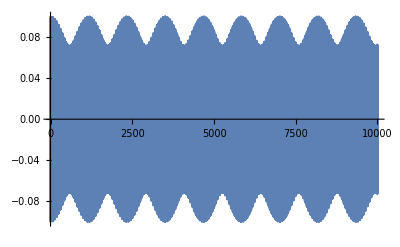

```mathematica
ListPlot[tableb,Joined->True,PlotRange->All]
```

```mathematica
x= tablea[[All,2]];
y=tableb[[All,2]];
```

```mathematica
Show[{ploty,plotx}]
```

Show::gcomb: Could not combine the graphics objects in Show[{ploty,plotx}].

Show[{ploty,plotx}]

```mathematica
xwind=Table[(Sin[i π/100000])^2 x[[i]],{i,0,100000}];
ywind=Table[(Sin[i π/100000])^2 y[[i]],{i,0,100000}];
```

```mathematica
listfourierx=Abs[Fourier[xwind/.{wx->10,γ->π/4,wy->10}]];
listfouriery=Abs[Fourier[ywind/.{wx->10,γ->π/4,wy->10,α->0}]];
```

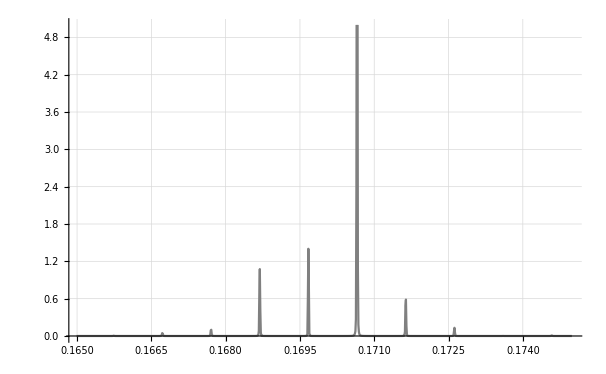

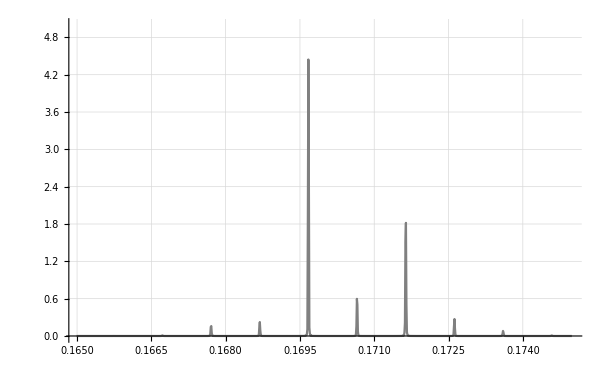

```mathematica
ListPlot[Table[{(n1-1)/(100000),listfourierx[[n1]]},{n1,1,100001}][[Range[16500,17500]]],PlotStyle->Gray,PlotRange->{0,5},Joined->True,GridLines->Automatic] 
ListPlot[Table[{(n1-1)/(100000),listfouriery[[n1]]},{n1,1,100001}][[Range[16500,17500]]],PlotStyle->Gray,PlotRange->{0,5},Joined->True,GridLines->Automatic]
```

```mathematica
inloc=inputpr/.{Jxv->a^2/100,Jyv->b^2/100,ϕxv->ϕa,ϕyv->ϕb,f2->50,k11->-10,k12->-15,p->0,r->0,q->0,η->0.001,k1->.0,k2->.0,νx->.1705,νy->.1695,wr->.1715,n->t};
tablesol=Flatten[NDSolve[inloc/.{a->0.1,b->.1,ϕa->π,ϕb->0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,100000}]];
```

```mathematica
podsum=(10(Sqrt[Jx[t]/.(tablesol)]/.{t->t1})Cos[2π νx0 n+ϕa+(ϕx[t]/.(tablesol))/.{t->t1}])/.{νx0->0.1705,n->t1,ϕa->π,ϕb->0};
```

```mathematica
tablea=Table[{t1,podsum},{t1,0,100000,1}];
```

```mathematica
ListPlot[tablea,Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
podsumb=(10(Sqrt[Jy[t]/.(tablesol)]/.{t->t1})Cos[2π νy0 n+ϕb+(ϕy[t]/.(tablesol))/.{t->t1}])/.{νy0->0.1695,n->t1,ϕa->π,ϕb->0};
```

```mathematica
tableb=Table[{t1,podsumb},{t1,0,100000,1}];
```

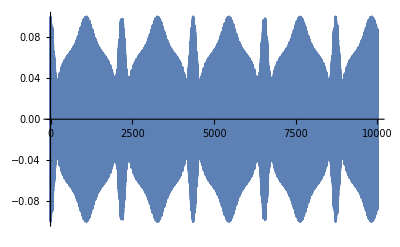

```mathematica
ListPlot[tableb,Joined->True,PlotRange->All]
```

```mathematica
a1=wx Cos[γ];
a1c=wx Cos[γ];
a3=wy Sin[γ] ;
a3c=wy Sin[γ];
b1=-Sin[γ]wx ;
b1c=-Sin[γ]wx ;
b3=wy Cos[γ];
b3c=wy Cos[γ] ;
```

```mathematica
x=a1 tablea[[All,2]]+b1 tableb[[All,2]];
y=a3 tablea[[All,2]]+b3 tableb[[All,2]];
```

```mathematica
x= tablea[[All,2]];
y=tableb[[All,2]];
```

```mathematica
Show[{ploty,plotx}]
```

Show::gcomb: Could not combine the graphics objects in Show[{ploty,plotx}].

Show[{ploty,plotx}]

```mathematica
xwind=Table[(Sin[i π/100000])^2 x[[i]],{i,0,100000}];
ywind=Table[(Sin[i π/100000])^2 y[[i]],{i,0,100000}];
```

```mathematica
listfourierx=Abs[Fourier[xwind/.{wx->10,γ->π/4,wy->10}]];
listfouriery=Abs[Fourier[ywind/.{wx->10,γ->π/4,wy->10,α->0}]];
```

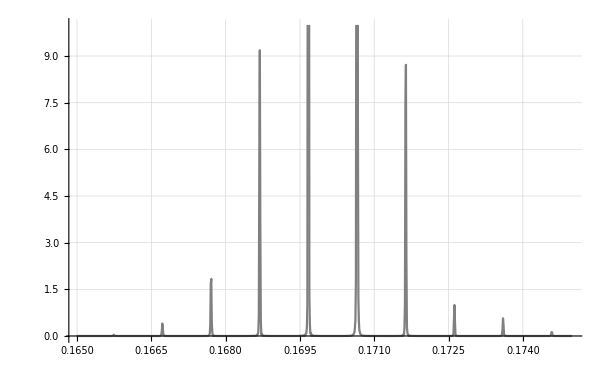

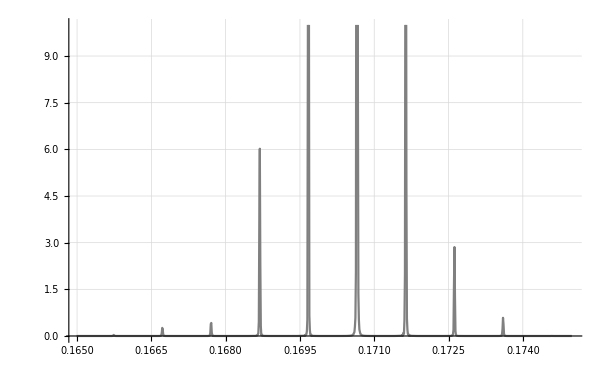

```mathematica
ListPlot[Table[{(n1-1)/(100000),listfourierx[[n1]]},{n1,1,100001}][[Range[16500,17500]]],PlotStyle->Gray,PlotRange->{0,10},Joined->True,GridLines->Automatic] 
ListPlot[Table[{(n1-1)/(100000),listfouriery[[n1]]},{n1,1,100001}][[Range[16500,17500]]],PlotStyle->Gray,PlotRange->{0,10},Joined->True,GridLines->Automatic]
```

```mathematica
inloc=inputpr/.{Jxv->a^2/100,Jyv->b^2/100,ϕxv->ϕa,ϕyv->ϕb,f2->50,k11->-10,k12->-15,p->0,r->0,q->-0,η->0.001,k1->.001,k2->.001,νx->.1705,νy->.1695,wr->.1716,n->t};
tablesol=Flatten[NDSolve[inloc/.{a->0.1,b->.1,ϕa->π,ϕb->0},{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,100000}]];
```

```mathematica
podsum=(10(Sqrt[Jx[t]/.(tablesol)]/.{t->t1})Cos[2π νx0 n+ϕa+(ϕx[t]/.(tablesol))/.{t->t1}])/.{νx0->0.1705,n->t1,ϕa->π,ϕb->0};
```

```mathematica
tablea=Table[{t1,podsum},{t1,0,100000,1}];
```

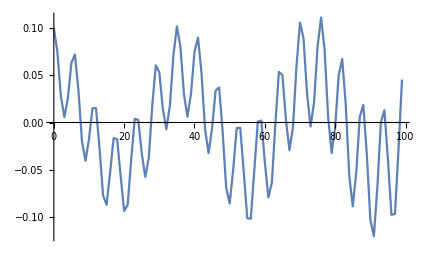

```mathematica
ListPlot[tablea[[Range[0,100]]],Joined->True,PlotRange->All]
```

```mathematica
podsumb=(10(Sqrt[Jy[t]/.(tablesol)]/.{t->t1})Cos[2π νy0 n+ϕb+(ϕy[t]/.(tablesol))/.{t->t1}])/.{νy0->0.1695,n->t1,ϕa->π,ϕb->0};
```

```mathematica
tableb=Table[{t1,podsumb},{t1,0,100000,1}];
```

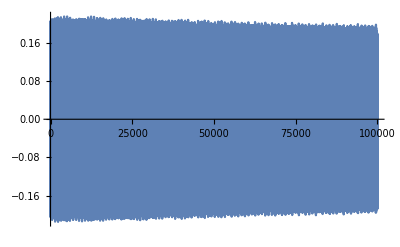

```mathematica
ListPlot[tableb,Joined->True,PlotRange->All]
```

```mathematica
x= tablea[[All,2]];
y=tableb[[All,2]];
```

```mathematica
Show[{ploty,plotx}]
```

Show::gcomb: Could not combine the graphics objects in Show[{ploty,plotx}].

Show[{ploty,plotx}]

```mathematica
xwind=Table[(Sin[i π/100000])^2 x[[i]],{i,0,100000}];
ywind=Table[(Sin[i π/100000])^2 y[[i]],{i,0,100000}];
```

```mathematica
listfourierx=Abs[Fourier[xwind/.{wx->10,γ->π/4,wy->10}]];
listfouriery=Abs[Fourier[ywind/.{wx->10,γ->π/4,wy->10,α->0}]];
```

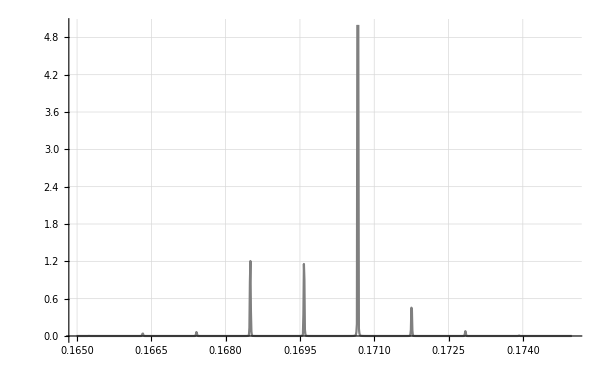

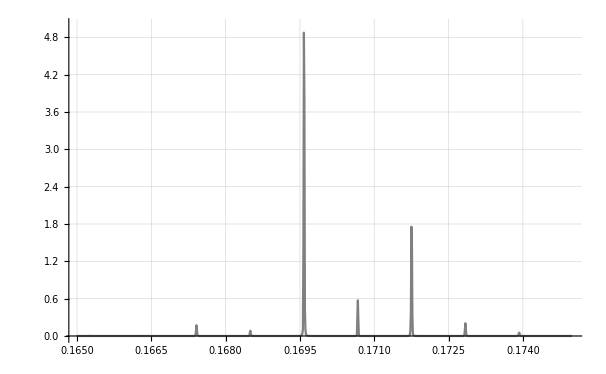

```mathematica
ListPlot[Table[{(n1-1)/(100000),listfourierx[[n1]]},{n1,1,100001}][[Range[16500,17500]]],PlotStyle->Gray,PlotRange->{0,5},Joined->True,GridLines->Automatic] 
ListPlot[Table[{(n1-1)/(100000),listfouriery[[n1]]},{n1,1,100001}][[Range[16500,17500]]],PlotStyle->Gray,PlotRange->{0,5},Joined->True,GridLines->Automatic]
```

```mathematica
эффект от раскачки почему то такой - для малых амплитуд раскачки меняет расстояние между пиками, для больших - сдвигает пики
```